Semion_Monte Carlo simulation
Compare results of different initial state of MCMC
Compare the distribution functions of MCMC, Yongshi Wu and spinful Femion

```mathematica
FermiDistr[Level_,mu_,Tem_]:=Module[{ni,energy},
energy=Level-1;
ni=1/(Exp[(energy-mu)/Tem]+1);
ni
]

TotalParNum[mu_,maxsum_,Tem_]:=Module[{N,k,ek},
N=0; (*N is the total particle number*) 
For[k=1,k≤maxsum,k++,  (*k is the level number with the energy of the ground/1st level being zero.*)
N=N+FermiDistr[k,mu,Tem];
];
N
]

(*Nump is the total number of particles*)
ChemicalEnergy[Nump_,Ef_,Tem_]:=Module[{tol,maxsum,mutry,k,ek,mumin,mumax,nexit,nmax,Ntry,tol1,mu},
(*Print[Nump];*)
tol=10^(-12);
maxsum=0;
mutry=Ef+Tem;
For[k=Ef+1,k≤Ef+1000,k++,
If[FermiDistr[k,mutry,Tem]≤tol,{maxsum=k;Break[]},0];
];
mumin=If[Tem≥0.5,Ef-3*Tem,Ef-1];
mumax=If[Tem≥0.5,Ef+Tem,Ef+1];
Ntry=TotalParNum[mutry,maxsum,Tem];
tol1=10^(-6);
nmax=1000;
nexit=1;
While[Abs[Ntry-Nump]>tol1,
If[nexit==nmax,{Print["error"];Break[]}];
If[Ntry-Nump<0,{mumin=mutry},{mumax=mutry}];
mutry=0.5*(mumin+mumax);
Ntry=TotalParNum[mutry,maxsum,Tem];
(*Print[Ntry];*)
(*Print[Abs[Ntry-Nump]];*)
nexit=nexit+1;
];
mu=mutry;
mu
]

WuDistrSemion[level_,mu_,Tem_]:=Module[{ni,ei},
ei=level-1;
ni=1/Sqrt[1/4+Exp[2*(ei-mu)/Tem]];
ni
]


TotalParNumSemion[mu_,maxsum_,Tem_]:=Module[{N,k,ek},
N=0; (*N is the total particle number*) 
For[k=1,k≤maxsum,k++, (*k is the level number with the energy of the ground/1st level being zero.*)
N=N+WuDistrSemion[k,mu,Tem];
];
N
]

ChemicalEnergyWu[Nump_,Ef_,Tem_]:=Module[{tol,maxsum,mutry,k,ek,mumin,mumax,mutry1,Ntry,tol1,mu,nmax,nexit},
(*Print[Nump];*)
tol=10^(-12);
maxsum=0;
mutry=Ef+Tem;
For[k=Ef+1,k≤Ef+1000,k++,
If[WuDistrSemion[k,mutry,Tem]≤tol,{maxsum=k;Break[]},0];
];
mumin=If[Tem≥0.5,Ef-3*Tem,Ef-1];
mumax=If[Tem≥0.5,Ef+Tem,Ef+1];
Ntry=TotalParNumSemion[mutry,maxsum,Tem];
tol1=10^(-6);
nmax=1000;
nexit=1;
While[Abs[Ntry-Nump]>tol1,
If[nexit==nmax,{Print["error"];Break[]}];
If[Ntry-Nump<0,{mumin=mutry},{mumax=mutry}];
mutry=0.5*(mumin+mumax);
Ntry=TotalParNumSemion[mutry,maxsum,Tem];
(*Print[Ntry];*)
(*Print[Abs[Ntry-Nump]];*)
nexit=nexit+1;
];
mu=mutry;
mu
]
```

C:\Users\bohsi\Documents

Data importing finished

Ground state:

{2,2,2,2,2,2,2,2,2,2,2,2,0,0,0,0,0,0,0,0,0,0}

Excitation state 1:

{2,2,2,2,2,2,2,0,0,2,2,2,0,1,1,0,2,0,0,0,0,0}

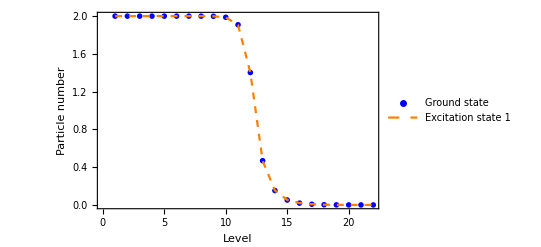

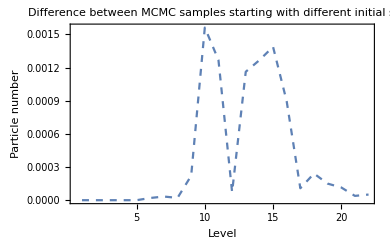

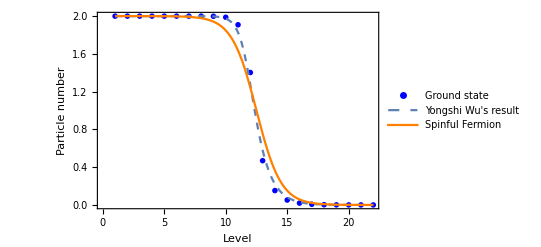

MCMC:

{2.,2.,2.,2.,2.,1.99998,1.99994,1.99969,1.99842,1.98789,1.90839,1.40279,0.468753,0.152231,0.051922,0.019353,0.007236,0.002294,0.000818,0.000211,0.000071,0.000017}

WuDistrSemion:

{2.,2.,2.,2.,2.,1.99999,1.99993,1.99951,1.99636,1.97358,1.8264,1.27221,0.580452,0.221765,0.0820198,0.0301954,0.0111093,0.00408695,0.00150351,0.00055311,0.000203478,0.0000748553}

2*FermiDistr:

{1.99998,1.99994,1.99985,1.99959,1.99889,1.997,1.99186,1.97803,1.94138,1.84828,1.63515,1.24492,0.755079,0.364849,0.151716,0.0586241,0.0219738,0.00814023,0.00300235,0.00110555,0.000406852,0.000149692}

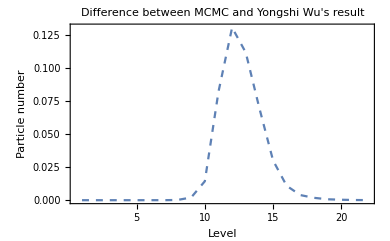

```mathematica
Directory[]
Tem=1.0;
NumTotal=24;
Ef=11; (*Fermi level is 12; Fermi energy is 11*)
muFermion=ChemicalEnergy[NumTotal/2,Ef,Tem];
muWu=ChemicalEnergyWu[NumTotal,Ef,Tem];


StateMatrixE6=Import["data_e6.txt","Table"];
StateMatrix1E6=Import["data1_e6.txt","Table"];
Print["Data importing finished"];

stateMatrixSize=10^6;
stateSize=22;
NpMC=Table[0,{i,1,stateSize}];
For[i=1,i≤stateSize,i++,
NpMC[[i]]=Total[StateMatrixE6[[All,i]]]/stateMatrixSize
];
NpMC1=Table[0,{i,1,stateSize}];
For[i=1,i≤stateSize,i++,
NpMC1[[i]]=Total[StateMatrix1E6[[All,i]]]/stateMatrixSize
];
Diff=Abs[NpMC1-NpMC];


NpMCPlot=Table[0,{i,1,stateSize}];
NpMC1Plot=Table[0,{i,1,stateSize}];
DiffPlot=Table[0,{i,1,stateSize}];
For[i=1,i≤stateSize,i++,
NpMCPlot[[i]]={i,NpMC[[i]]};
NpMC1Plot[[i]]={i,NpMC1[[i]]};
DiffPlot[[i]]={i,Diff[[i]]};
];

Print["Ground state:"];
Print[StateMatrixE6[[1]]];
Print["Excitation state 1:"];
Print[StateMatrix1E6[[1]]];

plot1=ListPlot[NpMCPlot,Frame->True,FrameLabel->{"Level","Particle number"},PlotRange->{0,2},PlotStyle->{Blue},PlotMarkers->{"*",20},PlotLegends->{"Ground state"}];
plot2=ListLinePlot[NpMC1Plot,Frame->True,FrameLabel->{"Level","Particle number"},PlotRange->{0,2},PlotStyle->{Dashed,Orange},PlotLegends->{"Excitation state 1"}];
Print[Show[plot1,plot2]];
ListLinePlot[DiffPlot,Frame->True,FrameLabel->{"Level","Particle number"},PlotRange->All,PlotStyle->{Dashed},PlotLabel->"Difference between MCMC samples starting with different initial state"]



plot3=Plot[WuDistrSemion[x,muWu,Tem],{x,1,stateSize},Frame->True,FrameLabel->{"Level","Particle number"},PlotRange->{0,2},PlotStyle->{Dashed},PlotLegends->{"Yongshi Wu's result"}];
plot4=Plot[2*FermiDistr[y,muFermion,Tem],{y,1,stateSize},Frame->True,FrameLabel->{"Level","Particle number"},PlotRange->{0,2},PlotStyle->{Orange},PlotLegends->{"Spinful Fermion"}];
Print[Show[plot1,plot3,plot4]];
Print["MCMC:"]
Print[N[NpMC]]
Print["WuDistrSemion:"]
Print[WuDistrSemion[Table[i,{i,1,stateSize}],muWu,Tem]]
Print["2*FermiDistr:"]
Print[2*FermiDistr[Table[i,{i,1,stateSize}],muFermion,Tem]]

Diff1=Table[0,{i,1,stateSize}];
Diff1Plot=Table[0,{i,1,stateSize}];
For[i=1,i≤stateSize,i++,
Diff1[[i]]=Abs[WuDistrSemion[i,muWu,Tem]-NpMC[[i]]];
Diff1Plot[[i]]={i,Diff1[[i]]};
];
ListLinePlot[Diff1Plot,Frame->True,FrameLabel->{"Level","Particle number"},PlotRange->All,PlotStyle->{Dashed},PlotLabel->"Difference between MCMC and Yongshi Wu's result"]
```